```mathematica
(* Stochastic Germination calculations *)
```

```mathematica
(* follows Johnston,Iain G. and George W.Bassel. "Identification of a bet-hedging network motif generating noise in hormone concentrations and germination propensity in Arabidopsis." Journal of the Royal Society Interface 15.141 (2018):20180042. *)
```

```mathematica
(* note that throughout this notebook, the species "A" is denoted "p[t]"; "S" is denoted "e[t]"; "D" is denoted "d[t]" *)
```

```mathematica
(* each section follows a similar format -- the stoichiometric matrix, reaction rates, and species are defined, the system size expansion is used to produce ODEs for means and (co)variances, and these ODEs are solved. these individual steps are commented in the first section only. *)
```

## Simple, symmetric model

```mathematica
(* stoichiometric matrix, reaction rates, and species *)
```

```mathematica
s = Transpose[{{0, 1, 0}, {0, 0, 1}, {0, -1, 0}, {0, 0, -1}, {1, 0, 0}, {-1, 0, 0}}];
rates = {β p[t], β p[t], δ e[t], δ d[t], λ  (Λ e[t] +1), ν p[t] (Λ d[t]+ 1)};
r = {p[t], e[t], d[t]};
```

```mathematica
(* number of species and reactions *)
```

```mathematica
nt = 3;
nr = 6;
```

```mathematica
(* matrices A and B in the Fokker-Planck equation arising from the system size expansion *)
```

```mathematica
amatrix = Simplify[Table[Table[D[(s.rates)[[i]], r[[k]]], {k, 1, nt}], {i, 1, nt}]]
```

{{-ν (1+Λ d[t]),λ Λ,-Λ ν p[t]},{β,-δ,0},{β,0,-δ}}

```mathematica
bmatrix= Simplify[Table[Table[Sum[s[[i]][[j]] s[[k]][[j]] rates[[j]], {j, 1, nr}], {k, 1, nt}], {i, 1, nt}]]
```

{{λ+λ Λ e[t]+(ν+Λ ν d[t]) p[t],0,0},{0,δ e[t]+β p[t],0},{0,0,δ d[t]+β p[t]}}

```mathematica
(* labels associated with (co)variances *)
```

```mathematica
ξs = {{ξpp[t], ξep[t], ξdp[t]},{ξep[t], ξee[t],  ξde[t]},{ξdp[t], ξde[t], ξdd[t]}};
```

```mathematica
(* the time derivatives ("deebuh dee tees") of the (co)variance terms, from the Fokker-Planck equation *)
```

```mathematica
deebuhs = Simplify[Table[Table[Sum[amatrix[[k]][[i]] ξs[[i]][[l]], {i, 1, nt}]+Sum[amatrix[[l]][[j]] ξs[[k]][[j]], {j, 1, nt}]+bmatrix[[k]][[l]], {l, 1, nt}], {k, 1, nt}]];
```

```mathematica
(* corresponding ODEs for the time behaviour of means and (co)variances *)
```

```mathematica
meaneqns = Flatten[Union[Table[D[r[[i]],t] == (s.rates)[[i]], {i, 1, nt}]]]
```

{d'[t]==-δ d[t]+β p[t],e'[t]==-δ e[t]+β p[t],p'[t]==λ (1+Λ e[t])-ν (1+Λ d[t]) p[t]}

```mathematica
vareqns = Union[Flatten[Table[Table[D[ξs[[i]][[j]],t] == deebuhs[[i]][[j]], {i, 1, nt}], {j, 1, nt}]]]
```

{ξdd'[t]==δ d[t]+β p[t]-2 δ ξdd[t]+2 β ξdp[t],ξde'[t]==-2 δ ξde[t]+β (ξdp[t]+ξep[t]),ξdp'[t]==-Λ ν p[t] ξdd[t]+λ Λ ξde[t]-δ ξdp[t]-ν (1+Λ d[t]) ξdp[t]+β ξpp[t],ξee'[t]==δ e[t]+β p[t]-2 δ ξee[t]+2 β ξep[t],ξep'[t]==-Λ ν p[t] ξde[t]+λ Λ ξee[t]-δ ξep[t]-ν (1+Λ d[t]) ξep[t]+β ξpp[t],ξpp'[t]==λ+λ Λ e[t]+ν p[t] (1+Λ d[t]-2 Λ ξdp[t])+2 λ Λ ξep[t]-2 ν ξpp[t]-2 Λ ν d[t] ξpp[t]}

```mathematica
(* Eqns S3-S5 *)
```

```mathematica
meaneqns // TableForm
```

d'[t]==-δ d[t]+β p[t]
e'[t]==-δ e[t]+β p[t]
p'[t]==λ (1+Λ e[t])-ν (1+Λ d[t]) p[t]

```mathematica
(* Eqns S6-S11 *)
```

```mathematica
vareqns//TableForm
```

ξdd'[t]==δ d[t]+β p[t]-2 δ ξdd[t]+2 β ξdp[t]
ξde'[t]==-2 δ ξde[t]+β (ξdp[t]+ξep[t])
ξdp'[t]==-Λ ν p[t] ξdd[t]+λ Λ ξde[t]-δ ξdp[t]-ν (1+Λ d[t]) ξdp[t]+β ξpp[t]
ξee'[t]==δ e[t]+β p[t]-2 δ ξee[t]+2 β ξep[t]
ξep'[t]==-Λ ν p[t] ξde[t]+λ Λ ξee[t]-δ ξep[t]-ν (1+Λ d[t]) ξep[t]+β ξpp[t]
ξpp'[t]==λ+λ Λ e[t]+ν p[t] (1+Λ d[t]-2 Λ ξdp[t])+2 λ Λ ξep[t]-2 ν ξpp[t]-2 Λ ν d[t] ξpp[t]

```mathematica
(* solve and extract informations from these ODEs. the rest of the sections basically repeat this process for different chemical-kinetic systems *)
```

```mathematica
msoln=FullSimplify[Solve[meaneqns/.d'[t]->0/.e'[t]->0/.p'[t]->0,{d[t],e[t],p[t]}]][[2]]
```

{d[t]→(β λ)/(δ ν),e[t]→(β λ)/(δ ν),p[t]→λ/ν}

```mathematica
(d[t]/p[t])/.msoln
Simplify[(e[t]/p[t])/.msoln]
```

β/δ

β/δ

```mathematica
varianceeqns = Flatten[Union[vareqns]]
```

{ξdd'[t]==δ d[t]+β p[t]-2 δ ξdd[t]+2 β ξdp[t],ξde'[t]==-2 δ ξde[t]+β (ξdp[t]+ξep[t]),ξdp'[t]==-Λ ν p[t] ξdd[t]+λ Λ ξde[t]-δ ξdp[t]-ν (1+Λ d[t]) ξdp[t]+β ξpp[t],ξee'[t]==δ e[t]+β p[t]-2 δ ξee[t]+2 β ξep[t],ξep'[t]==-Λ ν p[t] ξde[t]+λ Λ ξee[t]-δ ξep[t]-ν (1+Λ d[t]) ξep[t]+β ξpp[t],ξpp'[t]==λ+λ Λ e[t]+ν p[t] (1+Λ d[t]-2 Λ ξdp[t])+2 λ Λ ξep[t]-2 ν ξpp[t]-2 Λ ν d[t] ξpp[t]}

```mathematica
vsoln=Simplify[Solve[varianceeqns/.ξdd'[t]->0/.ξde'[t]-> 0/.ξdp'[t]->0/.ξee'[t]->0 /.ξep'[t]->0/.ξpp'[t]->0,{ ξdd[t],ξde[t],ξdp[t],ξee[t],ξep[t],ξpp[t]}]];
```

```mathematica
vpp = ((ξpp[t]/.vsoln[[1]])/.msoln);
```

```mathematica
(* Eqns 2.7, 2.8 *)
```

```mathematica
msoln
```

{d[t]→(β λ)/(δ ν),e[t]→(β λ)/(δ ν),p[t]→λ/ν}

```mathematica
(* Eqn 2.9 *)
```

```mathematica
ξa2=Simplify[vpp]
```

(λ (β^2 λ^2 Λ^2+δ^2 ν (δ+ν)+β δ λ Λ (δ+2 (λ Λ+ν))))/(ν (β λ Λ+δ ν) (δ^2+β λ Λ+δ ν))

```mathematica
η = Sqrt[ξa2]/(p[t]/.msoln)
```

(ν √((λ (β^2 λ^2 Λ^2+δ^2 ν (δ+ν)+β δ λ Λ (δ+2 (λ Λ+ν))))/(ν (β λ Λ+δ ν) (δ^2+β λ Λ+δ ν))))/λ

```mathematica
(* show that derivative is always positive *)
```

```mathematica
ddΛ = Simplify[D[ξa2, Λ]]
```

(2 β δ^2 λ^3 Λ (2 δ ν (δ+ν)+β λ Λ (δ+2 ν)))/(ν (β λ Λ+δ ν)^2 (δ^2+β λ Λ+δ ν)^2)

```mathematica
(* Eqn 2.10 *)
```

```mathematica
Limit[ξa2,Λ->∞]
```

((β+2 δ) λ)/(β ν)

```mathematica
ddβ = Simplify[D[ξa2, β]]
```

(2 δ λ^3 Λ^2 (-β^2 λ^2 Λ^2+δ^2 ν (δ+ν)))/(ν (β λ Λ+δ ν)^2 (δ^2+β λ Λ+δ ν)^2)

```mathematica
solnβ=FullSimplify[Solve[ddβ == 0, β],  Assumptions->{ν∈Reals, δ∈Reals, ν>0, δ>0}]
```

{{β→-(δ √(ν (δ+ν)))/(λ Λ)},{β→(δ √(ν (δ+ν)))/(λ Λ)}}

```mathematica
(* Eqn 2.11 *)
```

```mathematica
FullSimplify[ξa2/.solnβ[[2]]]
```

(λ (δ^2+2 δ λ Λ+4 λ Λ (ν-√(ν (δ+ν)))))/(δ^2 ν)

```mathematica
(* confirm structure of Fig 2 *)
```

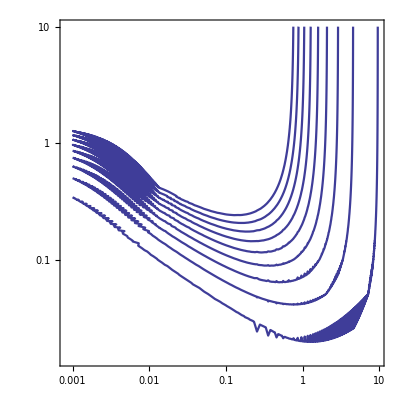

```mathematica
pl=Normal@ContourPlot[η/.β->lβ/.Λ->lΛ/.δ->1/.λ->10/.ν->0.1, {lβ, 0.001, 10}, {lΛ, 0.001, 10}, PlotPoints->100];
ListLogLogPlot[Cases[pl,Line[a_,b___]:>a,Infinity],Joined->True,Frame->True,PlotRange->All,AspectRatio->1,PlotStyle->ColorData[1][1]]
```

## Asymmetric model with δ = 1

```mathematica
s = Transpose[{{0, 1, 0}, {0, 0, 1}, {0, -1, 0}, {0, 0, -1}, {1, 0, 0}, {-1, 0, 0}}];
rates = {βs p[t], βd p[t],  e[t],  d[t], λ  (Λs e[t] +1), ν p[t] (Λd d[t]+ 1)};
r = {p[t], e[t], d[t]};
```

```mathematica
nt = 3;
nr = 6;
```

```mathematica
amatrix = Simplify[Table[Table[D[(s.rates)[[i]], r[[k]]], {k, 1, nt}], {i, 1, nt}]]
```

{{-ν (1+Λd d[t]),λ Λs,-Λd ν p[t]},{βs,-1,0},{βd,0,-1}}

```mathematica
bmatrix= Simplify[Table[Table[Sum[s[[i]][[j]] s[[k]][[j]] rates[[j]], {j, 1, nr}], {k, 1, nt}], {i, 1, nt}]]
```

{{λ+λ Λs e[t]+(ν+Λd ν d[t]) p[t],0,0},{0,e[t]+βs p[t],0},{0,0,d[t]+βd p[t]}}

```mathematica
meaneqns = Flatten[Union[Table[D[r[[i]],t] == (s.rates)[[i]], {i, 1, nt}]]]
```

{d'[t]==-d[t]+βd p[t],e'[t]==-e[t]+βs p[t],p'[t]==λ (1+Λs e[t])-ν (1+Λd d[t]) p[t]}

```mathematica
ξs = {{ξpp[t], ξep[t], ξdp[t]},{ξep[t], ξee[t],  ξde[t]},{ξdp[t], ξde[t], ξdd[t]}};
```

```mathematica
deebuhs = Simplify[Table[Table[Sum[amatrix[[k]][[i]] ξs[[i]][[l]], {i, 1, nt}]+Sum[amatrix[[l]][[j]] ξs[[k]][[j]], {j, 1, nt}]+bmatrix[[k]][[l]], {l, 1, nt}], {k, 1, nt}]];
```

```mathematica
vareqns = Union[Flatten[Table[Table[D[ξs[[i]][[j]],t] == deebuhs[[i]][[j]], {i, 1, nt}], {j, 1, nt}]]]
```

{ξdd'[t]==d[t]+βd p[t]-2 ξdd[t]+2 βd ξdp[t],ξde'[t]==-2 ξde[t]+βs ξdp[t]+βd ξep[t],ξdp'[t]==-Λd ν p[t] ξdd[t]+λ Λs ξde[t]-ξdp[t]-ν (1+Λd d[t]) ξdp[t]+βd ξpp[t],ξee'[t]==e[t]+βs p[t]-2 ξee[t]+2 βs ξep[t],ξep'[t]==-Λd ν p[t] ξde[t]+λ Λs ξee[t]-ξep[t]-ν (1+Λd d[t]) ξep[t]+βs ξpp[t],ξpp'[t]==λ+λ Λs e[t]+ν p[t] (1+Λd d[t]-2 Λd ξdp[t])+2 λ Λs ξep[t]-2 ν ξpp[t]-2 Λd ν d[t] ξpp[t]}

```mathematica
msoln=FullSimplify[Solve[meaneqns/.d'[t]->0/.e'[t]->0/.p'[t]->0,{d[t],e[t],p[t]}]][[1]]
```

{d[t]→(βs λ Λs-ν+√(4 βd λ Λd ν+(-βs λ Λs+ν)^2))/(2 Λd ν),e[t]→(βs (βs λ Λs-ν+√(4 βd λ Λd ν+(-βs λ Λs+ν)^2)))/(2 βd Λd ν),p[t]→(βs λ Λs-ν+√(4 βd λ Λd ν+(-βs λ Λs+ν)^2))/(2 βd Λd ν)}

```mathematica
(d[t]/p[t])/.msoln
Simplify[(e[t]/p[t])/.msoln]
```

βd

βs

```mathematica
varianceeqns = Flatten[Union[vareqns]]
```

{ξdd'[t]==d[t]+βd p[t]-2 ξdd[t]+2 βd ξdp[t],ξde'[t]==-2 ξde[t]+βs ξdp[t]+βd ξep[t],ξdp'[t]==-Λd ν p[t] ξdd[t]+λ Λs ξde[t]-ξdp[t]-ν (1+Λd d[t]) ξdp[t]+βd ξpp[t],ξee'[t]==e[t]+βs p[t]-2 ξee[t]+2 βs ξep[t],ξep'[t]==-Λd ν p[t] ξde[t]+λ Λs ξee[t]-ξep[t]-ν (1+Λd d[t]) ξep[t]+βs ξpp[t],ξpp'[t]==λ+λ Λs e[t]+ν p[t] (1+Λd d[t]-2 Λd ξdp[t])+2 λ Λs ξep[t]-2 ν ξpp[t]-2 Λd ν d[t] ξpp[t]}

```mathematica
vsoln=Simplify[Solve[varianceeqns/.ξdd'[t]->0/.ξde'[t]-> 0/.ξdp'[t]->0/.ξee'[t]->0 /.ξep'[t]->0/.ξpp'[t]->0,{ ξdd[t],ξde[t],ξdp[t],ξee[t],ξep[t],ξpp[t]}]];
```

```mathematica
(* Eqn 2.12 *)
```

```mathematica
generalm = p[t]/.msoln
```

(βs λ Λs-ν+√(4 βd λ Λd ν+(-βs λ Λs+ν)^2))/(2 βd Λd ν)

```mathematica
(* Eqn 2.13 *)
```

```mathematica
generalv = ξa2 = FullSimplify[(ξpp[t]/.vsoln[[1]])/.d[t]->βd p[t]/.e[t]->βs p[t]]
```

(λ (1-βs λ Λs+ν)+p[t] (βs λ Λs (1-(-2+βs) λ Λs)+ν+2 βd λ Λd ν+ν^2+βd Λd ν p[t] (1+βs λ Λs+3 ν+2 (1+βd) Λd ν p[t])))/(2 (1+ν+βd Λd ν p[t]) (-βs λ Λs+ν+2 βd Λd ν p[t]))

```mathematica
(*** check that we reduce to the symmetric model ***)
```

```mathematica
Simplify[p[t]/.msoln/.{Λs->Λ,Λd->Λ,δd->δ,δs->δ,βd->β,βs->β},  Assumptions->{β>0, Λ>0, λ>0, ν>0, δ>0}]
```

λ/ν

```mathematica
Simplify[Simplify[ξa2/.p[t]->λ/ν/.{Λs->Λ,Λd->Λ,δd->δ,δs->δ,βd->β,βs->β}]/.√((β λ Λ+ν)^2)->(β λ Λ+δ ν), Assumptions->{β>0, Λ>0, λ>0, ν>0, δ>0}]
```

(λ (β^2 λ^2 Λ^2+ν (1+ν)+β λ Λ (1+2 λ Λ+2 ν)))/(ν (β λ Λ+ν) (1+β λ Λ+ν))

## Changes to parameters in asymmetric model

```mathematica
m = p[t]/.msoln
```

(βs λ Λs-ν+√(4 βd λ Λd ν+(-βs λ Λs+ν)^2))/(2 βd Λd ν)

```mathematica
v = Simplify[ξa2/.msoln];
```

```mathematica
s = Sqrt[v]/m;
```

```mathematica
subs = {βs->0.1, βd->0.1, δ->1, λ->10, ν->0.1, Λs->0.1, Λd->0.1};
```

```mathematica
trace = Table[{}, {i, 1, 12}];
```

```mathematica
max = 0.35;
```

```mathematica
trace[[1]] = Table[{Log10[m],s}/.Λs->tmp/.subs, {tmp, 0.0001,max, 0.05}];
trace[[2]] = Table[{Log10[m],s}/.Λd->tmp/.subs, {tmp, 0.01, max, 0.05}];
trace[[3]]= Table[{Log10[m],s}/.βs->tmp/.subs, {tmp, 0.0001, max, 0.05}];
trace[[4]]= Table[{Log10[m],s}/.βd->tmp/.subs, {tmp, 0.01, max, 0.05}];
trace[[5]]= Table[{Log10[m],s}/.Λs->tmp/.Λd->tmp/.subs, {tmp, 0.000001, max, 0.05}];
trace[[6]]= Table[{Log10[m],s}/.βs->tmp/.βd->tmp/.subs, {tmp, 0.0001, max, 0.05}];
trace[[7]]= Table[{Log10[m],s}/.βs->0.1-0.1*tmp/.Λs->tmp/.subs, {tmp, 0.0001, 2max, 0.05}];
trace[[8]]= Table[{Log10[m],s}/.βd->0.1-0.1*tmp/.Λd->tmp/.subs, {tmp, 0.01,2 max, 0.05}];
trace[[9]]= Table[{Log10[m],s}/.βs->0.1-0.1*tmp/.Λd->tmp/.subs, {tmp, 0.01,max, 0.05}];
trace[[10]]= Table[{Log10[m],s}/.βd->0.1-0.1*tmp/.Λs->tmp/.subs, {tmp, 0.0001, max, 0.05}];
trace[[11]]= Table[{Log10[m],s}/.Λs->tmp/.Λd->0.1*tmp/.subs, {tmp, 0.000001, max, 0.05}];
trace[[12]]= Table[{Log10[m],s}/.Λs->0.1*tmp/.Λd->tmp/.subs, {tmp, 0.000001, max, 0.05}];
```

```mathematica
labels = {"Λ_s^+", "Λ_d^+", "β_s^+", "β_d^+", "Λ_s^+, Λ_d^+", "β_s^+, β_d^+", "β_s^-, Λ_s^+", "β_d^-, Λ_d^+", "β_s^-, Λ_d^+", "β_d^-, Λ_s^+", "Λ_s^(++), Λ_d^+",  "Λ_s^+, Λ_d^(++)"};
```

```mathematica
mycolor[x_]:=RGBColor[x^2, 1-x, 1-x^2]
```

```mathematica
legend = Table[{mycolor[i/12], Text[Style[ToString[i]<>"^+: "<>labels[[i]],FontSize->18], {3.2, 0.22-i/(6*12)}]}, {i, 1, 12}];
```

```mathematica
xtrace = Table[{Log10[x], Sqrt[x]/x}, {x, 40,800, 10}];
```

```mathematica
(* Figure 4b *)
```

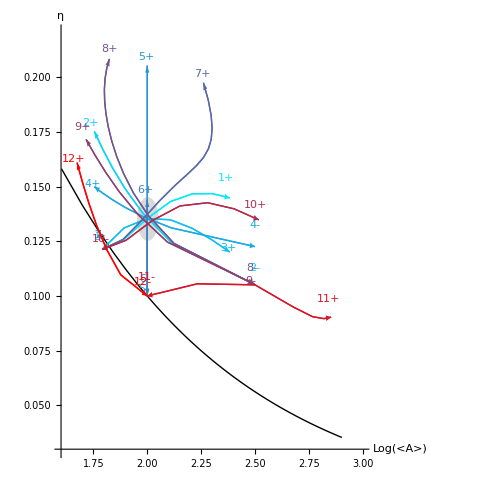

```mathematica
Graphics[Flatten[{LightGray,Disk[{Log10[m],s}/.subs, {0.05, 0.01}],White,Rectangle[{2.55,0.148},{2.85,0.22}], legend,Thick,Black,Line[xtrace],Arrowheads[{-0.04,0.04}],Table[{mycolor[i/12],Line[trace[[i]]],Arrow[trace[[i]]],Text[ToString[i]<>"+",trace[[i]][[-1]]+{-0.01+RandomReal[{-0.01,0.01}],0.005+RandomReal[{-0.005, 0.005}]}],Text[ToString[i]<>"-", trace[[i]][[1]]+{-0.01+RandomReal[{-0.01,0.01}],0.005+RandomReal[{-0.005, 0.005}]}]}, {i, 1, 12}]}], Axes->True, AxesStyle->Thick,TicksStyle->Larger,LabelStyle->Large,AspectRatio->1, AxesOrigin->{1.6,0.03}, PlotRange->{{1.6,3}, {0.03,0.22}},AxesLabel->{"Log(<A>)", "η"}, ImageSize->500, BaseStyle->{Medium}]
```

```mathematica
(* Eqn 2.14 *)
```

```mathematica
mρ=m/.Λs->0/.√(4 βd λ Λd ν+ν^2)->ρ
```

(-ν+ρ)/(2 βd Λd ν)

```mathematica
(* Eqn 2.15 *)
```

```mathematica
tmp = ξa2/.p[t]->m;
vρ=FullSimplify[Simplify[tmp/.Λs->0]/.√(ν (4 βd λ Λd+ν))->ρ/.(1/√(ν (4 βd λ Λd+ν)))->1/ρ]
```

(2 βd^2 λ Λd (1+ρ)+βd λ Λd (-3 ν+ρ)+ν (-ν+ρ))/(βd^2 Λd ρ (2+ν+ρ))

```mathematica
(* confirm that η' drops below 1 *)
```

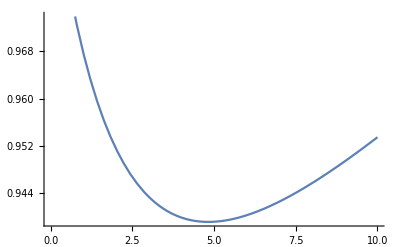

```mathematica
Plot[Sqrt[v]/Sqrt[m] /.Λs->0/.βd->0.1/.λ->0.1/.ν->0.1, {Λd, 0, 10}]
```

## Direct feedback, symmetric

```mathematica
s = Transpose[{ {1, 0, 0}, {-1, 0, 0}}];
rates = { λ (Λ  p[t] +1), ν p[t] (Λ p[t]+ 1)};
r = {p[t]};
```

```mathematica
nt = 1;
nr = 2;
```

```mathematica
amatrix = Simplify[Table[Table[D[(s.rates)[[i]], r[[k]]], {k, 1, nt}], {i, 1, nt}]]
```

{{λ Λ-ν-2 Λ ν p[t]}}

```mathematica
bmatrix= Simplify[Table[Table[Sum[s[[i]][[j]] s[[k]][[j]] rates[[j]], {j, 1, nr}], {k, 1, nt}], {i, 1, nt}]]
```

{{(1+Λ p[t]) (λ+ν p[t])}}

```mathematica
ξs = {{ξpp[t]}};
```

```mathematica
deebuhs = Simplify[Table[Table[Sum[amatrix[[k]][[i]] ξs[[i]][[l]], {i, 1, nt}]+Sum[amatrix[[l]][[j]] ξs[[k]][[j]], {j, 1, nt}]+bmatrix[[k]][[l]], {l, 1, nt}], {k, 1, nt}]];
```

```mathematica
vareqns = Union[Flatten[Table[Table[D[ξs[[i]][[j]],t] == deebuhs[[i]][[j]], {i, 1, nt}], {j, 1, nt}]]]
```

{ξpp'[t]==(1+Λ p[t]) (λ+ν p[t])+2 (λ Λ-ν-2 Λ ν p[t]) ξpp[t]}

```mathematica
meaneqns = Flatten[Union[Table[D[r[[i]],t] == (s.rates)[[i]], {i, 1, nt}]]]
```

{p'[t]==λ (1+Λ p[t])-ν p[t] (1+Λ p[t])}

```mathematica
msoln=FullSimplify[Solve[meaneqns/.d'[t]->0/.e'[t]->0/.p'[t]->0,{d[t],e[t],p[t]}]][[2]]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{p[t]→λ/ν}

```mathematica
varianceeqns = Flatten[Union[vareqns]]
```

{ξpp'[t]==(1+Λ p[t]) (λ+ν p[t])+2 (λ Λ-ν-2 Λ ν p[t]) ξpp[t]}

```mathematica
vsoln=Solve[varianceeqns/.ξdd'[t]->0/.ξde'[t]-> 0/.ξdp'[t]->0/.ξee'[t]->0 /.ξep'[t]->0/.ξpp'[t]->0,{ ξdd[t],ξde[t],ξdp[t],ξee[t],ξep[t],ξpp[t]}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{ξpp[t]→-((1+Λ p[t]) (λ+ν p[t]))/(2 (λ Λ-ν-2 Λ ν p[t]))}}

```mathematica
vpp = ((ξpp[t]/.vsoln[[1]])/.msoln);
```

```mathematica
(* Eqn 2.22 *)
```

```mathematica
p[t]/.msoln
ξa2 = FullSimplify[vpp]
```

λ/ν

λ/ν

## Single pathway, symmetric

```mathematica
s = Transpose[{{0, 1, 0}, {0, -1, 0}, {1, 0, 0}, {-1, 0, 0}}];
rates = {β p[t], δ e[t], λ (Λ e[t] +1), ν p[t] (Λ e[t]+ 1)};
r = {p[t], e[t]};
```

```mathematica
nt = 2;
nr = 4;
```

```mathematica
amatrix = Simplify[Table[Table[D[(s.rates)[[i]], r[[k]]], {k, 1, nt}], {i, 1, nt}]]
```

{{-ν (1+Λ e[t]),Λ (λ-ν p[t])},{β,-δ}}

```mathematica
bmatrix= Simplify[Table[Table[Sum[s[[i]][[j]] s[[k]][[j]] rates[[j]], {j, 1, nr}], {k, 1, nt}], {i, 1, nt}]]
```

{{(1+Λ e[t]) (λ+ν p[t]),0},{0,δ e[t]+β p[t]}}

```mathematica
ξs = {{ξpp[t], ξep[t]},{ξep[t], ξee[t]}};
```

```mathematica
deebuhs = Simplify[Table[Table[Sum[amatrix[[k]][[i]] ξs[[i]][[l]], {i, 1, nt}]+Sum[amatrix[[l]][[j]] ξs[[k]][[j]], {j, 1, nt}]+bmatrix[[k]][[l]], {l, 1, nt}], {k, 1, nt}]];
```

```mathematica
vareqns = Union[Flatten[Table[Table[D[ξs[[i]][[j]],t] == deebuhs[[i]][[j]], {i, 1, nt}], {j, 1, nt}]]]
```

{ξee'[t]==δ e[t]+β p[t]-2 δ ξee[t]+2 β ξep[t],ξep'[t]==Λ (λ-ν p[t]) ξee[t]-(δ+ν+Λ ν e[t]) ξep[t]+β ξpp[t],ξpp'[t]==(1+Λ e[t]) (λ+ν p[t])+2 Λ (λ-ν p[t]) ξep[t]-2 ν (1+Λ e[t]) ξpp[t]}

```mathematica
meaneqns = Flatten[Union[Table[D[r[[i]],t] == (s.rates)[[i]], {i, 1, nt}]]]
```

{e'[t]==-δ e[t]+β p[t],p'[t]==λ (1+Λ e[t])-ν (1+Λ e[t]) p[t]}

```mathematica
msoln=FullSimplify[Solve[meaneqns/.d'[t]->0/.e'[t]->0/.p'[t]->0,{d[t],e[t],p[t]}]][[2]]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{e[t]→(β λ)/(δ ν),p[t]→λ/ν}

```mathematica
e[t]/p[t] /.msoln
```

β/δ

```mathematica
varianceeqns = Flatten[Union[vareqns]]
```

{ξee'[t]==δ e[t]+β p[t]-2 δ ξee[t]+2 β ξep[t],ξep'[t]==Λ (λ-ν p[t]) ξee[t]-(δ+ν+Λ ν e[t]) ξep[t]+β ξpp[t],ξpp'[t]==(1+Λ e[t]) (λ+ν p[t])+2 Λ (λ-ν p[t]) ξep[t]-2 ν (1+Λ e[t]) ξpp[t]}

```mathematica
vsoln=Solve[varianceeqns/.ξdd'[t]->0/.ξde'[t]-> 0/.ξdp'[t]->0/.ξee'[t]->0 /.ξep'[t]->0/.ξpp'[t]->0,{ ξdd[t],ξde[t],ξdp[t],ξee[t],ξep[t],ξpp[t]}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{ξee[t]→-(-2 β^2 (1+Λ e[t]) (λ+ν p[t])-(-δ e[t]-β p[t]) (-2 ν (1+Λ e[t]) (δ+ν+Λ ν e[t])+2 β Λ (λ-ν p[t])))/(-4 β Λ ν (1+Λ e[t]) (λ-ν p[t])-2 δ (-2 ν (1+Λ e[t]) (δ+ν+Λ ν e[t])+2 β Λ (λ-ν p[t]))),ξep[t]→-((-β δ λ-β δ λ Λ e[t]-δ λ Λ ν e[t]-δ λ Λ^2 ν e[t]^2-β δ ν p[t]-β λ Λ ν p[t]-β δ Λ ν e[t] p[t]-β λ Λ^2 ν e[t] p[t]+δ Λ ν^2 e[t] p[t]+δ Λ^2 ν^2 e[t]^2 p[t]+β Λ ν^2 p[t]^2+β Λ^2 ν^2 e[t] p[t]^2)/(2 (δ+ν+Λ ν e[t]) (-β λ Λ+δ ν+δ Λ ν e[t]+β Λ ν p[t]))),ξpp[t]→-((-δ^2 λ+β λ^2 Λ-δ λ ν-δ^2 λ Λ e[t]+β λ^2 Λ^2 e[t]-δ λ^2 Λ^2 e[t]-2 δ λ Λ ν e[t]-δ λ Λ^2 ν e[t]^2-β λ^2 Λ^2 p[t]-δ^2 ν p[t]-δ ν^2 p[t]-δ^2 Λ ν e[t] p[t]+2 δ λ Λ^2 ν e[t] p[t]-2 δ Λ ν^2 e[t] p[t]-δ Λ^2 ν^2 e[t]^2 p[t]+2 β λ Λ^2 ν p[t]^2-β Λ ν^2 p[t]^2-β Λ^2 ν^2 e[t] p[t]^2-δ Λ^2 ν^2 e[t] p[t]^2-β Λ^2 ν^2 p[t]^3)/(2 (δ+ν+Λ ν e[t]) (-β λ Λ+δ ν+δ Λ ν e[t]+β Λ ν p[t])))}}

```mathematica
vpp = ((ξpp[t]/.vsoln[[1]])/.msoln);
```

```mathematica
(* Eqn 2.22 *)
```

```mathematica
p[t]/.msoln
FullSimplify[vpp]
```

λ/ν

λ/ν

## Direct feedback, asymmetric

```mathematica
s = Transpose[{ {1, 0, 0}, {-1, 0, 0}}];
rates = { λ (Λs p[t] +1), ν p[t] (Λd p[t]+ 1)};
r = {p[t]};
```

```mathematica
nt = 1;
nr = 2;
```

```mathematica
amatrix = Simplify[Table[Table[D[(s.rates)[[i]], r[[k]]], {k, 1, nt}], {i, 1, nt}]]
```

{{λ Λs-ν-2 Λd ν p[t]}}

```mathematica
bmatrix= Simplify[Table[Table[Sum[s[[i]][[j]] s[[k]][[j]] rates[[j]], {j, 1, nr}], {k, 1, nt}], {i, 1, nt}]]
```

{{λ+(λ Λs+ν) p[t]+Λd ν p[t]^2}}

```mathematica
ξs = {{ξpp[t]}};
```

```mathematica
deebuhs = Simplify[Table[Table[Sum[amatrix[[k]][[i]] ξs[[i]][[l]], {i, 1, nt}]+Sum[amatrix[[l]][[j]] ξs[[k]][[j]], {j, 1, nt}]+bmatrix[[k]][[l]], {l, 1, nt}], {k, 1, nt}]];
```

```mathematica
vareqns = Union[Flatten[Table[Table[D[ξs[[i]][[j]],t] == deebuhs[[i]][[j]], {i, 1, nt}], {j, 1, nt}]]]
```

{ξpp'[t]==λ+Λd ν p[t]^2+2 (λ Λs-ν) ξpp[t]+p[t] (λ Λs+ν-4 Λd ν ξpp[t])}

```mathematica
meaneqns = Flatten[Union[Table[D[r[[i]],t] == (s.rates)[[i]], {i, 1, nt}]]]
```

{p'[t]==-ν p[t] (1+Λd p[t])+λ (1+Λs p[t])}

```mathematica
msoln=FullSimplify[Solve[meaneqns/.d'[t]->0/.e'[t]->0/.p'[t]->0,{d[t],e[t],p[t]}]][[1]]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{p[t]→(λ Λs-ν+√(4 λ Λd ν+(-λ Λs+ν)^2))/(2 Λd ν)}

```mathematica
varianceeqns = Flatten[Union[vareqns]]
```

{ξpp'[t]==λ+Λd ν p[t]^2+2 (λ Λs-ν) ξpp[t]+p[t] (λ Λs+ν-4 Λd ν ξpp[t])}

```mathematica
vsoln=Solve[varianceeqns/.ξdd'[t]->0/.ξde'[t]-> 0/.ξdp'[t]->0/.ξee'[t]->0 /.ξep'[t]->0/.ξpp'[t]->0,{ ξdd[t],ξde[t],ξdp[t],ξee[t],ξep[t],ξpp[t]}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{ξpp[t]→-(λ+λ Λs p[t]+ν p[t]+Λd ν p[t]^2)/(2 (λ Λs-ν-2 Λd ν p[t]))}}

```mathematica
(* Eqns 2.23, 2.24 *)
```

```mathematica
mean = p[t]/.msoln
 ξpp[t]/.vsoln[[1]]
variance = ξpp[t]/.vsoln[[1]]/.p[t]->mean;
noise = Sqrt[variance]/mean;
scalednoise = Sqrt[mean]*noise;
```

(λ Λs-ν+√(4 λ Λd ν+(-λ Λs+ν)^2))/(2 Λd ν)

-(λ+λ Λs p[t]+ν p[t]+Λd ν p[t]^2)/(2 (λ Λs-ν-2 Λd ν p[t]))

```mathematica
mean/.Λs->0
Simplify[variance/.Λs->0]
```

(-ν+√(4 λ Λd ν+ν^2))/(2 Λd ν)

λ/(√(ν (4 λ Λd+ν)))

```mathematica
(* as Λd -> ∞ *)
```

```mathematica
limmean = Simplify[Sqrt[4λ Λd ν]/(2 Λd ν)]
limvar = Simplify[λ/Sqrt[ν 4 λ Λd]]
limcv = Simplify[Sqrt[limvar]/limmean]
limetaprime = Simplify[limcv Sqrt[limmean]]
```

λ/(√(λ Λd ν))

λ/(2 √(λ Λd ν))

1/(√2 √(λ/(√(λ Λd ν))))

1/(√2)

## Single pathway, asymmetric

```mathematica
s = Transpose[{{0, 1, 0}, {0, -1, 0}, {1, 0, 0}, {-1, 0, 0}}];
rates = {β p[t], δ e[t], λ (Λs e[t] +1), ν p[t] (Λd e[t]+ 1)};
r = {p[t], e[t]};
```

```mathematica
nt = 2;
nr = 4;
```

```mathematica
amatrix = Simplify[Table[Table[D[(s.rates)[[i]], r[[k]]], {k, 1, nt}], {i, 1, nt}]]
```

{{-ν (1+Λd e[t]),λ Λs-Λd ν p[t]},{β,-δ}}

```mathematica
bmatrix= Simplify[Table[Table[Sum[s[[i]][[j]] s[[k]][[j]] rates[[j]], {j, 1, nr}], {k, 1, nt}], {i, 1, nt}]]
```

{{λ+ν p[t]+e[t] (λ Λs+Λd ν p[t]),0},{0,δ e[t]+β p[t]}}

```mathematica
ξs = {{ξpp[t], ξep[t]},{ξep[t], ξee[t]}};
```

```mathematica
deebuhs = Simplify[Table[Table[Sum[amatrix[[k]][[i]] ξs[[i]][[l]], {i, 1, nt}]+Sum[amatrix[[l]][[j]] ξs[[k]][[j]], {j, 1, nt}]+bmatrix[[k]][[l]], {l, 1, nt}], {k, 1, nt}]];
```

```mathematica
vareqns = Union[Flatten[Table[Table[D[ξs[[i]][[j]],t] == deebuhs[[i]][[j]], {i, 1, nt}], {j, 1, nt}]]]
```

{ξee'[t]==δ e[t]+β p[t]-2 δ ξee[t]+2 β ξep[t],ξep'[t]==(λ Λs-Λd ν p[t]) ξee[t]-(δ+ν+Λd ν e[t]) ξep[t]+β ξpp[t],ξpp'[t]==λ+2 λ Λs ξep[t]+p[t] (ν-2 Λd ν ξep[t])-2 ν ξpp[t]+e[t] (λ Λs+Λd ν p[t]-2 Λd ν ξpp[t])}

```mathematica
meaneqns = Flatten[Union[Table[D[r[[i]],t] == (s.rates)[[i]], {i, 1, nt}]]]
```

{e'[t]==-δ e[t]+β p[t],p'[t]==λ (1+Λs e[t])-ν (1+Λd e[t]) p[t]}

```mathematica
msoln=FullSimplify[Solve[meaneqns/.d'[t]->0/.e'[t]->0/.p'[t]->0,{d[t],e[t],p[t]}]][[1]]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{e[t]→(β λ Λs-δ ν+√(4 β δ λ Λd ν+(β λ Λs-δ ν)^2))/(2 δ Λd ν),p[t]→(β λ Λs-δ ν+√(4 β δ λ Λd ν+(β λ Λs-δ ν)^2))/(2 β Λd ν)}

```mathematica
(* check that this is identical to Eqn 2.12 *)
```

```mathematica
p[t]/.msoln/.δ->1
```

(β λ Λs-ν+√((β λ Λs-ν)^2+4 β λ Λd ν))/(2 β Λd ν)

```mathematica
e[t]/p[t] /.msoln
```

β/δ

```mathematica
varianceeqns = Flatten[Union[vareqns]]
```

{ξee'[t]==δ e[t]+β p[t]-2 δ ξee[t]+2 β ξep[t],ξep'[t]==(λ Λs-Λd ν p[t]) ξee[t]-(δ+ν+Λd ν e[t]) ξep[t]+β ξpp[t],ξpp'[t]==λ+2 λ Λs ξep[t]+p[t] (ν-2 Λd ν ξep[t])-2 ν ξpp[t]+e[t] (λ Λs+Λd ν p[t]-2 Λd ν ξpp[t])}

```mathematica
vsoln=Solve[varianceeqns/.ξdd'[t]->0/.ξde'[t]-> 0/.ξdp'[t]->0/.ξee'[t]->0 /.ξep'[t]->0/.ξpp'[t]->0,{ ξdd[t],ξde[t],ξdp[t],ξee[t],ξep[t],ξpp[t]}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{ξee[t]→-(2 β^2 (-λ-λ Λs e[t]-ν p[t]-Λd ν e[t] p[t])-(-δ e[t]-β p[t]) (-(δ+ν+Λd ν e[t]) (2 ν+2 Λd ν e[t])-β (-2 λ Λs+2 Λd ν p[t])))/(2 β (2 ν+2 Λd ν e[t]) (-λ Λs+Λd ν p[t])-2 δ (-(δ+ν+Λd ν e[t]) (2 ν+2 Λd ν e[t])-β (-2 λ Λs+2 Λd ν p[t]))),ξep[t]→-((-β δ λ-β δ λ Λs e[t]-δ λ Λs ν e[t]-δ λ Λd Λs ν e[t]^2-β δ ν p[t]-β λ Λs ν p[t]-β δ Λd ν e[t] p[t]-β λ Λd Λs ν e[t] p[t]+δ Λd ν^2 e[t] p[t]+δ Λd^2 ν^2 e[t]^2 p[t]+β Λd ν^2 p[t]^2+β Λd^2 ν^2 e[t] p[t]^2)/(2 (δ+ν+Λd ν e[t]) (-β λ Λs+δ ν+δ Λd ν e[t]+β Λd ν p[t]))),ξpp[t]→-((-δ^2 λ+β λ^2 Λs-δ λ ν-δ^2 λ Λs e[t]+β λ^2 Λs^2 e[t]-δ λ^2 Λs^2 e[t]-δ λ Λd ν e[t]-δ λ Λs ν e[t]-δ λ Λd Λs ν e[t]^2-β λ^2 Λs^2 p[t]-δ^2 ν p[t]-β λ Λd ν p[t]+β λ Λs ν p[t]-δ ν^2 p[t]-δ^2 Λd ν e[t] p[t]+2 δ λ Λd Λs ν e[t] p[t]-2 δ Λd ν^2 e[t] p[t]-δ Λd^2 ν^2 e[t]^2 p[t]+2 β λ Λd Λs ν p[t]^2-β Λd ν^2 p[t]^2-β Λd^2 ν^2 e[t] p[t]^2-δ Λd^2 ν^2 e[t] p[t]^2-β Λd^2 ν^2 p[t]^3)/(2 (δ+ν+Λd ν e[t]) (-β λ Λs+δ ν+δ Λd ν e[t]+β Λd ν p[t])))}}

```mathematica
variance = FullSimplify[ (ξpp[t]/.vsoln[[1]])/.e[t]->β/δ p[t]/.δ->1]
```

(λ (1-β λ Λs+ν)+p[t] (β λ Λs (1-(-2+β) λ Λs)+ν+2 β λ Λd ν+ν^2+β Λd ν p[t] (1+(-4+β) λ Λs+3 ν+2 (1+β) Λd ν p[t])))/(2 (1+ν+β Λd ν p[t]) (-β λ Λs+ν+2 β Λd ν p[t]))

```mathematica
onepathv = variance;
onepathm = p[t]/.msoln/.δ->1
fullv = (onepathv/.p[t]->p[t]/.msoln)/.δ->1;
```

(β λ Λs-ν+√((β λ Λs-ν)^2+4 β λ Λd ν))/(2 β Λd ν)

```mathematica
(* compare with previous model, as in text and Eqn S12 *)
```

```mathematica
onepathm
generalm/.βs->β/.βd->β
ov =FullSimplify[Expand[onepathv/.p[t]->p]]
gv=FullSimplify[Expand[generalv/.βs->β/.βd->β/.p[t]->p]]
```

(β λ Λs-ν+√((β λ Λs-ν)^2+4 β λ Λd ν))/(2 β Λd ν)

(β λ Λs-ν+√(4 β λ Λd ν+(-β λ Λs+ν)^2))/(2 β Λd ν)

-(-β λ^2 Λs (1+p (-2+β) Λs)+p ν (1+ν+p β Λd (1+(3+2 p (1+β) Λd) ν))+λ (1+ν+p β (Λs+Λd (2+p (-4+β) Λs) ν)))/(2 (β λ Λs-ν-2 p β Λd ν) (1+ν+p β Λd ν))

-(-β λ^2 Λs (1+p (-2+β) Λs)+p ν (1+ν+p β Λd (1+(3+2 p (1+β) Λd) ν))+λ (1+ν+p β (Λs+Λd (2+p β Λs) ν)))/(2 (β λ Λs-ν-2 p β Λd ν) (1+ν+p β Λd ν))

## Most general model (exploring different parameterisations)

```mathematica
s = Transpose[{{0, 1, 0}, {0, 0, 1}, {0, -1, 0}, {0, 0, -1}, {1, 0, 0}, {-1, 0, 0}}];
rates = {βs p[t], βd p[t], δs e[t], δd d[t], λ  (Λs e[t] +1), ν p[t] (Λd d[t]+ 1)};
r = {p[t], e[t], d[t]};
```

```mathematica
nt = 3;
nr = 6;
```

```mathematica
amatrix = Simplify[Table[Table[D[(s.rates)[[i]], r[[k]]], {k, 1, nt}], {i, 1, nt}]]
```

{{-ν (1+Λd d[t]),λ Λs,-Λd ν p[t]},{βs,-δs,0},{βd,0,-δd}}

```mathematica
bmatrix= Simplify[Table[Table[Sum[s[[i]][[j]] s[[k]][[j]] rates[[j]], {j, 1, nr}], {k, 1, nt}], {i, 1, nt}]]
```

{{λ+λ Λs e[t]+(ν+Λd ν d[t]) p[t],0,0},{0,δs e[t]+βs p[t],0},{0,0,δd d[t]+βd p[t]}}

```mathematica
ξs = {{ξpp[t], ξep[t], ξdp[t]},{ξep[t], ξee[t],  ξde[t]},{ξdp[t], ξde[t], ξdd[t]}};
```

```mathematica
deebuhs = Simplify[Table[Table[Sum[amatrix[[k]][[i]] ξs[[i]][[l]], {i, 1, nt}]+Sum[amatrix[[l]][[j]] ξs[[k]][[j]], {j, 1, nt}]+bmatrix[[k]][[l]], {l, 1, nt}], {k, 1, nt}]];
```

```mathematica
vareqns = Union[Flatten[Table[Table[D[ξs[[i]][[j]],t] == deebuhs[[i]][[j]], {i, 1, nt}], {j, 1, nt}]]]
```

{ξdd'[t]==δd d[t]+βd p[t]-2 δd ξdd[t]+2 βd ξdp[t],ξde'[t]==-(δd+δs) ξde[t]+βs ξdp[t]+βd ξep[t],ξdp'[t]==-Λd ν p[t] ξdd[t]+λ Λs ξde[t]-δd ξdp[t]-ν (1+Λd d[t]) ξdp[t]+βd ξpp[t],ξee'[t]==δs e[t]+βs p[t]-2 δs ξee[t]+2 βs ξep[t],ξep'[t]==-Λd ν p[t] ξde[t]+λ Λs ξee[t]-δs ξep[t]-ν (1+Λd d[t]) ξep[t]+βs ξpp[t],ξpp'[t]==λ+λ Λs e[t]+ν p[t] (1+Λd d[t]-2 Λd ξdp[t])+2 λ Λs ξep[t]-2 ν ξpp[t]-2 Λd ν d[t] ξpp[t]}

```mathematica
meaneqns = Flatten[Union[Table[D[r[[i]],t] == (s.rates)[[i]], {i, 1, nt}]]]
```

{d'[t]==-δd d[t]+βd p[t],e'[t]==-δs e[t]+βs p[t],p'[t]==λ (1+Λs e[t])-ν (1+Λd d[t]) p[t]}

```mathematica
msoln=FullSimplify[Solve[meaneqns/.d'[t]->0/.e'[t]->0/.p'[t]->0,{d[t],e[t],p[t]}]][[1]]
```

{d[t]→(βs δd λ Λs-δd δs ν+√(4 βd δd δs^2 λ Λd ν+(βs δd λ Λs-δd δs ν)^2))/(2 δd δs Λd ν),e[t]→(βs (βs δd λ Λs-δd δs ν+√(4 βd δd δs^2 λ Λd ν+(βs δd λ Λs-δd δs ν)^2)))/(2 βd δs^2 Λd ν),p[t]→(βs δd λ Λs-δd δs ν+√(4 βd δd δs^2 λ Λd ν+(βs δd λ Λs-δd δs ν)^2))/(2 βd δs Λd ν)}

```mathematica
(d[t]/p[t])/.msoln
Simplify[(e[t]/p[t])/.msoln]
```

βd/δd

βs/δs

```mathematica
varianceeqns = Flatten[Union[vareqns]]
```

{ξdd'[t]==δd d[t]+βd p[t]-2 δd ξdd[t]+2 βd ξdp[t],ξde'[t]==-(δd+δs) ξde[t]+βs ξdp[t]+βd ξep[t],ξdp'[t]==-Λd ν p[t] ξdd[t]+λ Λs ξde[t]-δd ξdp[t]-ν (1+Λd d[t]) ξdp[t]+βd ξpp[t],ξee'[t]==δs e[t]+βs p[t]-2 δs ξee[t]+2 βs ξep[t],ξep'[t]==-Λd ν p[t] ξde[t]+λ Λs ξee[t]-δs ξep[t]-ν (1+Λd d[t]) ξep[t]+βs ξpp[t],ξpp'[t]==λ+λ Λs e[t]+ν p[t] (1+Λd d[t]-2 Λd ξdp[t])+2 λ Λs ξep[t]-2 ν ξpp[t]-2 Λd ν d[t] ξpp[t]}

```mathematica
vsoln=Simplify[Solve[varianceeqns/.ξdd'[t]->0/.ξde'[t]-> 0/.ξdp'[t]->0/.ξee'[t]->0 /.ξep'[t]->0/.ξpp'[t]->0,{ ξdd[t],ξde[t],ξdp[t],ξee[t],ξep[t],ξpp[t]}]];
```

```mathematica
varexp =  Simplify[((ξpp[t]/.vsoln[[1]]))]
vpp = Simplify[varexp/.msoln];
```

(δd^3 δs^2 λ+δd^2 δs^3 λ-βs δd^3 λ^2 Λs-βs δd^2 δs λ^2 Λs-βs δd δs^2 λ^2 Λs+βs^2 δd λ^3 Λs^2+δd^3 δs λ ν+2 δd^2 δs^2 λ ν+δd δs^3 λ ν-βs δd^2 λ^2 Λs ν-2 βs δd δs λ^2 Λs ν+δd^2 δs λ ν^2+δd δs^2 λ ν^2+βs δd^3 λ^2 Λs^2 p[t]+βs δd^2 δs λ^2 Λs^2 p[t]-βs^2 δd λ^3 Λs^3 p[t]+δd^3 δs^2 ν p[t]+δd^2 δs^3 ν p[t]+βd δd^2 δs λ Λd ν p[t]+βd δd δs^2 λ Λd ν p[t]+βd δs^3 λ Λd ν p[t]-βs δd^3 λ Λs ν p[t]-βs δd^2 δs λ Λs ν p[t]-βs δd δs^2 λ Λs ν p[t]-βd βs δd λ^2 Λd Λs ν p[t]-βd βs δs λ^2 Λd Λs ν p[t]+βs^2 δd λ^2 Λs^2 ν p[t]+βs δd^2 λ^2 Λs^2 ν p[t]+βs δd δs λ^2 Λs^2 ν p[t]+δd^3 δs ν^2 p[t]+2 δd^2 δs^2 ν^2 p[t]+δd δs^3 ν^2 p[t]+2 βd δd δs λ Λd ν^2 p[t]+βd δs^2 λ Λd ν^2 p[t]-βs δd^2 λ Λs ν^2 p[t]-2 βs δd δs λ Λs ν^2 p[t]+δd^2 δs ν^3 p[t]+δd δs^2 ν^3 p[t]+δd δs (δd+δs) Λd^3 ν^3 d[t]^3 p[t]+βd βs δs λ^2 Λd Λs^2 ν p[t]^2+βd δd^2 δs Λd ν^2 p[t]^2+βd δd δs^2 Λd ν^2 p[t]^2+βd δs^3 Λd ν^2 p[t]^2+βd^2 δs λ Λd^2 ν^2 p[t]^2-βd βs δd λ Λd Λs ν^2 p[t]^2-βd βs δs λ Λd Λs ν^2 p[t]^2+2 βd δd δs Λd ν^3 p[t]^2+βd δs^2 Λd ν^3 p[t]^2+βd δd δs^2 Λd^2 ν^2 p[t]^3+βd δs^3 Λd^2 ν^2 p[t]^3-βd βs δd λ Λd^2 Λs ν^2 p[t]^3+βd^2 δs Λd^2 ν^3 p[t]^3+βd δd δs Λd^2 ν^3 p[t]^3+βd δs^2 Λd^2 ν^3 p[t]^3+βd^2 δs Λd^3 ν^3 p[t]^4+Λd^2 ν^2 d[t]^2 (δd δs (δd+δs) λ+δd δs (δd+δs) λ Λs e[t]+δd (δd^2 δs+δs (δs^2-2 βs λ Λs+3 δs ν)+δd (2 δs^2-βs λ Λs+3 δs ν)) p[t]+δs (δd (δd+δs)+βd (2 δd+δs)) Λd ν p[t]^2)+λ Λs e[t] (δd (δd^2-βs λ Λs+δs ν+δd (δs+ν)) (δs^2-βs λ Λs+δs (λ Λs+ν))+βd Λd ν (δd^2 δs+δd (δs^2-βs λ Λs+2 δs ν)+δs (δs^2-βs λ Λs+δs (λ Λs+ν))) p[t]+βd^2 δs Λd^2 ν^2 p[t]^2)+Λd ν d[t] (δd λ (δd^2 δs+δs (δs^2-2 βs λ Λs+2 δs ν)+δd (2 δs^2-βs λ Λs+2 δs ν))+(βd δs^2 λ Λd ν+δd^3 (δs^2-βs λ Λs+2 δs ν)+δd (βs^2 λ^2 Λs^2-βs δs λ Λs (δs-λ Λs+4 ν)+δs ν (2 δs^2+2 βd λ Λd+3 δs ν))+δd^2 (δs^3+βs λ Λs (λ Λs-2 ν)+4 δs^2 ν+δs (-βs λ Λs+3 ν^2))) p[t]+Λd ν (δd (δs^2 (δs+ν)+δd (δs^2-βs λ Λs+δs ν))+βd (δd^2 δs+δs (δs^2-βs λ Λs+2 δs ν)+δd (δs^2-βs λ Λs+4 δs ν))) p[t]^2+βd δs (βd+2 δd+δs) Λd^2 ν^2 p[t]^3+λ Λs e[t] (δd (δd^2 δs+δs (δs^2-2 βs λ Λs+δs λ Λs+2 δs ν)+δd (2 δs^2-βs λ Λs+δs λ Λs+2 δs ν))+βd δs (2 δd+δs) Λd ν p[t])))/(2 (δd (δs+ν) (βs^2 λ^2 Λs^2+δs (δd+δs) ν (δd+ν)-βs λ Λs (δd^2+2 δs ν+δd (δs+ν)))+δd δs (δd+δs) Λd^3 ν^3 d[t]^3+βd Λd ν (δs (δs+ν) (-βs λ Λs+δs ν)+δd^2 (δs^2-βs λ Λs+2 δs ν)+δd (δs^3+2 δs^2 ν-βs λ Λs ν+2 δs ν^2)) p[t]+βd^2 δs Λd^2 ν^2 (δd+ν) p[t]^2+Λd^2 ν^2 d[t]^2 (δd (δd^2 δs+δs (δs^2-2 βs λ Λs+3 δs ν)+δd (2 δs^2-βs λ Λs+3 δs ν))+βd δs (2 δd+δs) Λd ν p[t])+Λd ν d[t] (δd (βs^2 λ^2 Λs^2-2 βs δs λ Λs (δs+2 ν)+δs^2 ν (2 δs+3 ν)+δd^2 (δs^2-βs λ Λs+2 δs ν)+δd (δs+ν) (δs^2-2 βs λ Λs+3 δs ν))+βd Λd ν (2 δd^2 δs+δs (δs^2-βs λ Λs+2 δs ν)+δd (2 δs^2-βs λ Λs+4 δs ν)) p[t]+βd^2 δs Λd^2 ν^2 p[t]^2)))

```mathematica
(*** check that we reduce to the symmetric model ***)
```

```mathematica
ans1=Simplify[Simplify[vpp/.{Λs->Λ,Λd->Λ,δd->δ,δs->δ,βd->β,βs->β}]/.√(δ^2 (β λ Λ+δ ν)^2)->δ (β λ Λ+δ ν)]
```

(λ (β^2 λ^2 Λ^2+δ^2 ν (δ+ν)+β δ λ Λ (δ+2 (λ Λ+ν))))/(ν (β λ Λ+δ ν) (δ^2+β λ Λ+δ ν))

```mathematica
mpp = p[t]/.msoln
```

(βs δd λ Λs-δd δs ν+√(4 βd δd δs^2 λ Λd ν+(βs δd λ Λs-δd δs ν)^2))/(2 βd δs Λd ν)

```mathematica
subs={βs->0.1,βd->0.1,δ->1,λ->10,ν->0.1,Λs->0.1,Λd->0.1}
```

{βs→0.1,βd→0.1,δ→1,λ→10,ν→0.1,Λs→0.1,Λd→0.1}

```mathematica
δdset = {};
For[x = 0.01, x < 100, x *= 2,
AppendTo[δdset, x];
];
```

```mathematica
meanlistd = noiselistd = scalednoiselistd ={};
meanlists = noiselists = scalednoiselists={};
For[i=1,i<=Length[δdset],i++,
tβs=RandomReal[]; tβd = RandomReal[]; tν = RandomReal[]; tλ=RandomReal[];  tΛs=RandomReal[]; tΛd = RandomReal[];
nummean=mpp/.βs->tβs/.βd->tβd/.ν->tν/.λ->tλ/.Λs->tΛs/.Λd->tΛd;
numnoise=(Sqrt[vpp]/mpp)/.βs->tβs/.βd->tβd/.ν->tν/.λ->tλ/.Λs->tΛs/.Λd->tΛd;
numscalednoise=(numnoise*Sqrt[mpp])/.βs->tβs/.βd->tβd/.ν->tν/.λ->tλ/.Λs->tΛs/.Λd->tΛd;
AppendTo[meanlistd, Table[{δdset[[i]], nummean/.δs->1/.δd->δdset[[i]]}, {i, 1, Length[δdset]}]];
AppendTo[noiselistd, Table[{δdset[[i]], numnoise/.δs->1/.δd->δdset[[i]]}, {i, 1, Length[δdset]}]];
AppendTo[scalednoiselistd, Table[{δdset[[i]], numscalednoise/.δs->1/.δd->δdset[[i]]}, {i, 1, Length[δdset]}]];
AppendTo[meanlists, Table[{δdset[[i]], nummean/.δd->1/.δs->δdset[[i]]}, {i, 1, Length[δdset]}]];
AppendTo[noiselists, Table[{δdset[[i]], numnoise/.δd->1/.δs->δdset[[i]]}, {i, 1, Length[δdset]}]];
AppendTo[scalednoiselists, Table[{δdset[[i]], numscalednoise/.δd->1/.δs->δdset[[i]]},{i, 1, Length[δdset]}]];
];
```

```mathematica
(* Approximate Fig S2 *)
```

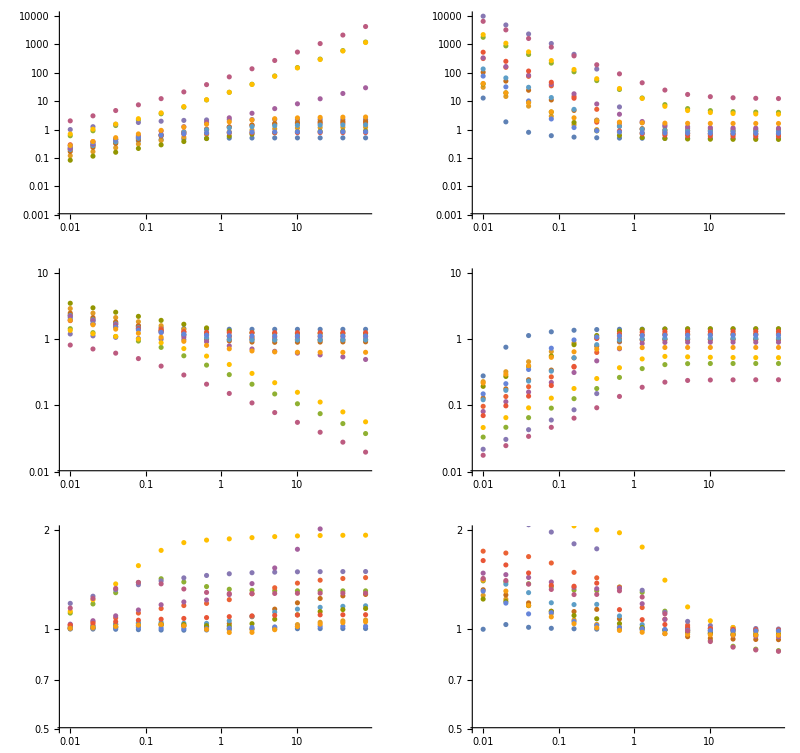

```mathematica
GraphicsGrid[{{ListLogLogPlot[meanlistd, PlotRange->{Automatic,{0.001, 10^4}}], ListLogLogPlot[meanlists,PlotRange->{Automatic,{0.001, 10^4}}]}, {ListLogLogPlot[noiselistd, PlotRange->{Automatic,{0.01, 10}}], ListLogLogPlot[noiselists, PlotRange->{Automatic,{0.01, 10}}]}, {ListLogLogPlot[scalednoiselistd, PlotRange->{Automatic,{0.5, 2}}], ListLogLogPlot[scalednoiselists, PlotRange->{Automatic,{0.5, 2}}]}}]
```